```mathematica
urqmdProcessesNN=Flatten[
Table[{{N938,h},{D1232,h}},
{h,
{
N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,N1900,N1990,N2080,N2190,N2220,N2250,
D1232,D1600,D1620,D1700,D1900,D1905,D1910,D1920,D1930,D1950
}
}],
1];
urqmdeCMNN=Table[2.3+3.7(ieCM/49.)^3,{ieCM,0,49}];
urqmdPartialSigmaNN=
{
{0.0759,0.0759,0.0762,0.0769,0.0784,0.0808,0.0845,0.0898,0.0973,0.1072,0.1203,0.1369,0.1574,0.1816,0.2092,0.2392,0.2708,0.3027,0.3341,0.3640,0.3918,0.4169,0.4389,0.4575,0.4726,0.4842,0.4922,0.4969,0.4983,0.4967,0.4924,0.4856,0.4766,0.4661,0.4537,0.4400,0.4253,0.4097,0.3936,0.3770,0.3603,0.3435,0.3268,0.3102,0.2941,0.2783,0.2629,0.2481,0.2338,0.2201},{0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0004,0.0005,0.0007,0.0010,0.0016,0.0026,0.0044,0.0076,0.0134,0.0244,0.0456,0.0859,0.0000,0.0009,0.0085,0.0498,0.1493,0.2903,0.4513,0.6164,0.7765,0.9262,1.0618,1.1815,1.2843,1.3704,1.4498,1.5063,1.5479,1.5754,1.5902,1.5933,1.5861,1.5697,1.5454,1.5143,1.4775,1.4362,1.3911,1.3433,1.2934,1.2421},{0.0055,0.0055,0.0056,0.0057,0.0058,0.0061,0.0065,0.0071,0.0081,0.0095,0.0117,0.0151,0.0204,0.0294,0.0453,0.0749,0.1316,0.2244,0.3410,0.4619,0.5697,0.6647,0.7461,0.8144,0.8699,0.9133,0.9453,0.9667,0.9797,0.9834,0.9794,0.9686,0.9519,0.9302,0.9044,0.8751,0.8433,0.8095,0.7743,0.7383,0.7020,0.6657,0.6298,0.5946,0.5603,0.5271,0.4951,0.4643,0.4350,0.4071},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0001,0.0002,0.0003,0.0004,0.0006,0.0010,0.0019,0.0039,0.0091,0.0238,0.0002,0.0059,0.0595,0.2646,0.5804,0.9215,1.2457,1.5365,1.7934,2.0098,2.1879,2.3285,2.4342,2.5075,2.5514,2.5692,2.5641,2.5391,2.4973,2.4415,2.3743,2.2981,2.2151,2.1271,2.0358,1.9426,1.8487,1.7552},{0.0132,0.0132,0.0132,0.0133,0.0134,0.0137,0.0141,0.0147,0.0155,0.0165,0.0180,0.0199,0.0226,0.0262,0.0315,0.0396,0.0526,0.0753,0.1127,0.1616,0.2136,0.2607,0.3010,0.3339,0.3599,0.3795,0.3932,0.4017,0.4055,0.4053,0.4020,0.3957,0.3869,0.3762,0.3638,0.3503,0.3359,0.3209,0.3055,0.2900,0.2746,0.2594,0.2445,0.2300,0.2160,0.2025,0.1896,0.1773,0.1657,0.1547},{0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0003,0.0004,0.0005,0.0007,0.0010,0.0014,0.0021,0.0030,0.0044,0.0065,0.0096,0.0142,0.0214,0.0335,0.0000,0.0002,0.0046,0.0410,0.1387,0.2641,0.3876,0.4969,0.5889,0.6640,0.7232,0.7675,0.7984,0.8175,0.8263,0.8263,0.8190,0.8055,0.7870,0.7645,0.7389,0.7111,0.6816,0.6512,0.6202,0.5891,0.5582,0.5279},{0.0055,0.0055,0.0055,0.0055,0.0056,0.0057,0.0058,0.0060,0.0063,0.0067,0.0071,0.0077,0.0085,0.0096,0.0110,0.0129,0.0155,0.0195,0.0257,0.0365,0.0559,0.0873,0.1255,0.1601,0.1893,0.2128,0.2310,0.2445,0.2539,0.2596,0.2620,0.2619,0.2595,0.2551,0.2491,0.2419,0.2337,0.2247,0.2152,0.2054,0.1954,0.1853,0.1753,0.1655,0.1559,0.1466,0.1376,0.1290,0.1208,0.1130},{0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0002,0.0002,0.0003,0.0004,0.0006,0.0008,0.0012,0.0017,0.0024,0.0035,0.0051,0.0073,0.0107,0.0159,0.0241,0.0000,0.0002,0.0056,0.0396,0.1011,0.1686,0.2311,0.2854,0.3304,0.3673,0.3958,0.4166,0.4306,0.4387,0.4415,0.4400,0.4348,0.4265,0.4158,0.4032,0.3891,0.3739,0.3580,0.3417,0.3252,0.3087},{0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0006,0.0006,0.0007,0.0009,0.0010,0.0013,0.0017,0.0024,0.0035,0.0055,0.0094,0.0179,0.0392,0.0957,0.1969,0.2998,0.3873,0.4604,0.5192,0.5653,0.6002,0.6251,0.6411,0.6504,0.6525,0.6489,0.6405,0.6280,0.6121,0.5935,0.5729,0.5506,0.5273,0.5033,0.4789,0.4545,0.4303,0.4066,0.3834,0.3609,0.3392,0.3184},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0002,0.0003,0.0006,0.0010,0.0020,0.0044,0.0116,0.0001,0.0038,0.0508,0.1866,0.3571,0.5248,0.6763,0.8089,0.9210,1.0129,1.0855,1.1401,1.1781,1.2014,1.2115,1.2103,1.1993,1.1801,1.1541,1.1225,1.0867,1.0476,1.0061,0.9632,0.9193},{0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0004,0.0004,0.0005,0.0006,0.0007,0.0010,0.0015,0.0022,0.0037,0.0066,0.0130,0.0295,0.0775,0.1803,0.2928,0.3886,0.4662,0.5279,0.5759,0.6117,0.6370,0.6538,0.6623,0.6639,0.6596,0.6503,0.6368,0.6199,0.6003,0.5786,0.5554,0.5311,0.5063,0.4812,0.4561,0.4313,0.4070,0.3834,0.3605,0.3385,0.3174},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0002,0.0003,0.0004,0.0006,0.0012,0.0028,0.0077,0.0000,0.0033,0.0484,0.1898,0.3681,0.5416,0.6966,0.8319,0.9445,1.0357,1.1066,1.1588,1.1941,1.2143,1.2212,1.2168,1.2027,1.1805,1.1517,1.1177,1.0797,1.0387,0.9956,0.9513,0.9064},{0.0001,0.0001,0.0001,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0003,0.0004,0.0006,0.0008,0.0011,0.0017,0.0025,0.0039,0.0064,0.0109,0.0208,0.0462,0.1040,0.1713,0.2273,0.2707,0.3037,0.3278,0.3446,0.3552,0.3610,0.3623,0.3600,0.3547,0.3470,0.3374,0.3262,0.3140,0.3009,0.2873,0.2734,0.2595,0.2456,0.2319,0.2185,0.2056,0.1931,0.1811,0.1696},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0003,0.0008,0.0018,0.0043,0.0106,0.0001,0.0036,0.0428,0.1295,0.2240,0.3091,0.3815,0.4408,0.4879,0.5237,0.5494,0.5661,0.5752,0.5776,0.5744,0.5666,0.5550,0.5403,0.5233,0.5044,0.4843,0.4633,0.4419,0.4203},{0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0003,0.0003,0.0004,0.0004,0.0005,0.0007,0.0009,0.0012,0.0017,0.0026,0.0041,0.0074,0.0154,0.0356,0.0674,0.0974,0.1226,0.1429,0.1588,0.1708,0.1796,0.1854,0.1889,0.1901,0.1895,0.1874,0.1840,0.1795,0.1742,0.1682,0.1618,0.1550,0.1480,0.1409,0.1337,0.1267,0.1197,0.1129,0.1063,0.1000,0.0939},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0002,0.0004,0.0007,0.0015,0.0031,0.0000,0.0001,0.0041,0.0305,0.0757,0.1237,0.1681,0.2067,0.2399,0.2669,0.2883,0.3044,0.3158,0.3230,0.3264,0.3266,0.3241,0.3192,0.3125,0.3042,0.2947,0.2843,0.2732,0.2617,0.2499},{0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0003,0.0003,0.0003,0.0004,0.0004,0.0005,0.0006,0.0008,0.0010,0.0014,0.0021,0.0034,0.0062,0.0145,0.0435,0.0995,0.1538,0.1989,0.2354,0.2645,0.2872,0.3042,0.3163,0.3244,0.3285,0.3293,0.3274,0.3230,0.3166,0.3086,0.2993,0.2890,0.2779,0.2663,0.2543,0.2422,0.2300,0.2180,0.2061,0.1946,0.1834,0.1725},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0003,0.0004,0.0007,0.0013,0.0026,0.0062,0.0001,0.0046,0.0420,0.1143,0.1945,0.2705,0.3387,0.3986,0.4490,0.4902,0.5227,0.5471,0.5640,0.5743,0.5787,0.5779,0.5726,0.5636,0.5514,0.5367,0.5200,0.5018,0.4825,0.4624},{0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0006,0.0006,0.0007,0.0008,0.0009,0.0010,0.0012,0.0015,0.0018,0.0023,0.0030,0.0040,0.0057,0.0084,0.0132,0.0222,0.0377,0.0567,0.0750,0.0909,0.1042,0.1150,0.1234,0.1297,0.1340,0.1368,0.1382,0.1382,0.1372,0.1354,0.1327,0.1295,0.1257,0.1216,0.1172,0.1126,0.1079,0.1031,0.0983,0.0935,0.0888,0.0842},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0002,0.0003,0.0004,0.0007,0.0012,0.0020,0.0033,0.0058,0.0105,0.0216,0.0000,0.0016,0.0126,0.0320,0.0541,0.0764,0.0968,0.1153,0.1311,0.1445,0.1558,0.1658,0.1727,0.1776,0.1807,0.1822,0.1822,0.1811,0.1788,0.1758,0.1719,0.1674},{0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0002,0.0002,0.0003,0.0005,0.0009,0.0018,0.0038,0.0089,0.0223,0.0472,0.0748,0.0984,0.1172,0.1316,0.1425,0.1503,0.1557,0.1590,0.1605,0.1605,0.1594,0.1573,0.1543,0.1507,0.1465,0.1419,0.1370,0.1319,0.1266,0.1212,0.1158,0.1104,0.1050},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0001,0.0002,0.0005,0.0011,0.0029,0.0091,0.0000,0.0008,0.0112,0.0322,0.0559,0.0786,0.0993,0.1175,0.1332,0.1475,0.1590,0.1682,0.1755,0.1810,0.1847,0.1869,0.1877,0.1873,0.1858,0.1834,0.1801},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0002,0.0003,0.0004,0.0005,0.0008,0.0012,0.0018,0.0029,0.0051,0.0094,0.0175,0.0306,0.0464,0.0615,0.0743,0.0846,0.0923,0.0980,0.1019,0.1042,0.1051,0.1049,0.1037,0.1018,0.0994,0.0965,0.0932,0.0896,0.0858,0.0819,0.0780,0.0741,0.0702,0.0664},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0002,0.0003,0.0007,0.0013,0.0025,0.0052,0.0126,0.0000,0.0024,0.0150,0.0337,0.0533,0.0718,0.0878,0.1012,0.1122,0.1208,0.1272,0.1325,0.1353,0.1366,0.1366,0.1354,0.1333,0.1304,0.1269,0.1229},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0005,0.0010,0.0023,0.0057,0.0147,0.0303,0.0472,0.0618,0.0735,0.0824,0.0890,0.0937,0.0968,0.0985,0.0991,0.0988,0.0977,0.0961,0.0939,0.0913,0.0884,0.0853,0.0820,0.0786,0.0751,0.0716},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0002,0.0004,0.0012,0.0038,0.0000,0.0002,0.0052,0.0185,0.0341,0.0495,0.0634,0.0754,0.0856,0.0940,0.1016,0.1070,0.1110,0.1138,0.1154,0.1160,0.1156,0.1146,0.1128},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0003,0.0007,0.0018,0.0052,0.0149,0.0313,0.0478,0.0612,0.0715,0.0791,0.0847,0.0884,0.0908,0.0920,0.0923,0.0917,0.0906,0.0889,0.0868,0.0843,0.0816,0.0787,0.0757,0.0725,0.0693},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0004,0.0011,0.0042,0.0000,0.0006,0.0080,0.0210,0.0349,0.0478,0.0593,0.0691,0.0774,0.0850,0.0907,0.0951,0.0984,0.1007,0.1020,0.1025,0.1022,0.1013},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0004,0.0010,0.0028,0.0085,0.0224,0.0400,0.0551,0.0669,0.0758,0.0823,0.0868,0.0898,0.0915,0.0921,0.0919,0.0909,0.0894,0.0874,0.0850,0.0823,0.0794,0.0763,0.0731,0.0699},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0003,0.0007,0.0024,0.0000,0.0002,0.0053,0.0183,0.0330,0.0470,0.0594,0.0701,0.0791,0.0871,0.0932,0.0980,0.1014,0.1037,0.1050,0.1054,0.1049,0.1038},{30.0597,30.0604,30.0649,30.0770,30.0997,30.1344,30.1801,30.2323,30.2817,30.3140,30.3094,30.2433,30.0878,29.8139,29.3940,28.8047,28.0301,27.0630,25.9069,24.5754,23.0917,21.4867,19.8137,18.0830,16.3436,14.6309,12.9764,11.4058,9.9391,8.5898,7.3657,6.2694,5.2993,4.4501,3.7144,3.0829,2.5456,2.0918,1.7115,1.3948,1.1327,0.9168,0.7400,0.5958,0.4786,0.3838,0.3072,0.2456,0.1961,0.1565},{0.0018,0.0019,0.0019,0.0019,0.0021,0.0023,0.0026,0.0000,0.0000,0.0000,0.0000,0.0001,0.0002,0.0007,0.0021,0.0061,0.0174,0.0478,0.1119,0.2115,0.3368,0.4767,0.6219,0.7650,0.9011,1.0269,1.1434,1.2445,1.3315,1.4037,1.4610,1.5040,1.5330,1.5491,1.5533,1.5466,1.5303,1.5055,1.4734,1.4352,1.3920,1.3448,1.2946,1.2422,1.1884,1.1339,1.0792,1.0249,0.9714,0.9190},{0.0017,0.0017,0.0017,0.0017,0.0018,0.0018,0.0019,0.0020,0.0022,0.0024,0.0027,0.0031,0.0038,0.0048,0.0063,0.0088,0.0131,0.0207,0.0348,0.0617,0.1123,0.1963,0.3071,0.4256,0.5375,0.6366,0.7211,0.7908,0.8464,0.8889,0.9193,0.9389,0.9489,0.9503,0.9444,0.9321,0.9146,0.8935,0.8683,0.8402,0.8101,0.7784,0.7457,0.7124,0.6789,0.6456,0.6127,0.5804,0.5489,0.5184},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0004,0.0006,0.0010,0.0021,0.0047,0.0115,0.0000,0.0002,0.0056,0.0352,0.0864,0.1450,0.2040,0.2587,0.3076,0.3498,0.3853,0.4144,0.4401,0.4578,0.4702,0.4777,0.4810,0.4804,0.4766,0.4700,0.4609,0.4500,0.4374,0.4236,0.4089},{0.0034,0.0034,0.0034,0.0035,0.0035,0.0035,0.0036,0.0037,0.0039,0.0041,0.0044,0.0048,0.0052,0.0059,0.0068,0.0080,0.0099,0.0130,0.0185,0.0299,0.0568,0.1211,0.2228,0.3315,0.4237,0.5004,0.5626,0.6117,0.6491,0.6760,0.6935,0.7034,0.7059,0.7023,0.6934,0.6801,0.6631,0.6432,0.6209,0.5970,0.5718,0.5459,0.5184,0.4921,0.4660,0.4403,0.4153,0.3910,0.3676,0.3451},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0002,0.0003,0.0004,0.0006,0.0009,0.0013,0.0019,0.0028,0.0043,0.0077,0.0000,0.0011,0.0151,0.0563,0.1091,0.1618,0.2101,0.2523,0.2888,0.3188,0.3427,0.3608,0.3737,0.3818,0.3857,0.3858,0.3828,0.3771,0.3691,0.3593,0.3481,0.3358,0.3227,0.3091,0.2952},{0.0009,0.0009,0.0009,0.0010,0.0010,0.0010,0.0011,0.0012,0.0014,0.0017,0.0021,0.0027,0.0037,0.0051,0.0072,0.0104,0.0152,0.0226,0.0341,0.0521,0.0811,0.1280,0.2001,0.2949,0.3993,0.5003,0.5910,0.6684,0.7318,0.7816,0.8185,0.8437,0.8585,0.8639,0.8613,0.8517,0.8364,0.8162,0.7922,0.7660,0.7370,0.7063,0.6747,0.6425,0.6102,0.5782,0.5466,0.5158,0.4859,0.4571},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0003,0.0007,0.0019,0.0047,0.0109,0.0241,0.0000,0.0004,0.0090,0.0413,0.0893,0.1418,0.1930,0.2400,0.2805,0.3146,0.3422,0.3638,0.3796,0.3904,0.3984,0.4004,0.3989,0.3942,0.3870,0.3777,0.3668,0.3545,0.3414,0.3276},{0.0026,0.0026,0.0026,0.0026,0.0027,0.0027,0.0027,0.0028,0.0029,0.0031,0.0032,0.0035,0.0037,0.0041,0.0046,0.0051,0.0059,0.0069,0.0083,0.0103,0.0133,0.0182,0.0270,0.0436,0.0742,0.1198,0.1700,0.2153,0.2529,0.2825,0.3048,0.3225,0.3330,0.3387,0.3403,0.3384,0.3337,0.3270,0.3182,0.3080,0.2967,0.2846,0.2720,0.2592,0.2462,0.2332,0.2205,0.2080,0.1959,0.1842},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0001,0.0002,0.0003,0.0004,0.0006,0.0008,0.0011,0.0016,0.0022,0.0031,0.0046,0.0075,0.0000,0.0001,0.0024,0.0152,0.0352,0.0563,0.0761,0.0932,0.1075,0.1191,0.1280,0.1352,0.1398,0.1425,0.1435,0.1432,0.1416,0.1390,0.1357,0.1317,0.1272,0.1224,0.1174},{0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0003,0.0003,0.0003,0.0004,0.0005,0.0007,0.0009,0.0015,0.0025,0.0047,0.0100,0.0248,0.0666,0.1534,0.2608,0.3615,0.4471,0.5171,0.5726,0.6152,0.6464,0.6675,0.6799,0.6849,0.6835,0.6768,0.6661,0.6514,0.6338,0.6139,0.5922,0.5692,0.5454,0.5211,0.4966,0.4722,0.4481,0.4244},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0001,0.0002,0.0003,0.0006,0.0017,0.0055,0.0000,0.0008,0.0135,0.0452,0.0840,0.1231,0.1591,0.1909,0.2180,0.2406,0.2605,0.2751,0.2858,0.2931,0.2973,0.2987,0.2978,0.2949,0.2901,0.2840,0.2767,0.2685},{0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0004,0.0004,0.0004,0.0005,0.0006,0.0007,0.0008,0.0010,0.0013,0.0018,0.0025,0.0035,0.0053,0.0084,0.0143,0.0264,0.0511,0.0906,0.1341,0.1724,0.2046,0.2286,0.2465,0.2591,0.2672,0.2714,0.2724,0.2707,0.2671,0.2615,0.2546,0.2465,0.2376,0.2281,0.2182,0.2081,0.1979,0.1877,0.1777,0.1679,0.1584},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0002,0.0003,0.0006,0.0010,0.0019,0.0038,0.0000,0.0001,0.0037,0.0163,0.0329,0.0495,0.0643,0.0770,0.0875,0.0958,0.1028,0.1076,0.1108,0.1126,0.1133,0.1129,0.1116,0.1096,0.1070,0.1039,0.1005,0.0969},{0.0003,0.0003,0.0003,0.0003,0.0004,0.0004,0.0004,0.0004,0.0004,0.0004,0.0005,0.0005,0.0006,0.0007,0.0008,0.0010,0.0013,0.0017,0.0022,0.0031,0.0044,0.0066,0.0105,0.0178,0.0327,0.0669,0.1390,0.2369,0.3238,0.3926,0.4447,0.4818,0.5082,0.5249,0.5333,0.5350,0.5318,0.5239,0.5125,0.4982,0.4818,0.4637,0.4446,0.4248,0.4045,0.3842,0.3641,0.3442,0.3248,0.3060},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0004,0.0007,0.0012,0.0023,0.0047,0.0106,0.0001,0.0045,0.0285,0.0630,0.0970,0.1270,0.1521,0.1724,0.1890,0.2012,0.2099,0.2154,0.2182,0.2187,0.2172,0.2141,0.2096,0.2041,0.1978,0.1909,0.1835},{0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0004,0.0005,0.0006,0.0009,0.0013,0.0021,0.0036,0.0068,0.0144,0.0348,0.0871,0.1682,0.2508,0.3210,0.3774,0.4214,0.4545,0.4782,0.4941,0.5031,0.5065,0.5050,0.4999,0.4914,0.4801,0.4668,0.4518,0.4355,0.4183,0.4006,0.3825,0.3644,0.3463,0.3284},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0003,0.0007,0.0016,0.0043,0.0000,0.0004,0.0085,0.0311,0.0586,0.0859,0.1106,0.1322,0.1504,0.1654,0.1786,0.1881,0.1950,0.1996,0.2021,0.2027,0.2018,0.1996,0.1962,0.1918,0.1867},{0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0003,0.0004,0.0005,0.0007,0.0011,0.0018,0.0032,0.0060,0.0125,0.0294,0.0778,0.1741,0.2809,0.3713,0.4430,0.4983,0.5400,0.5701,0.5904,0.6026,0.6078,0.6075,0.6022,0.5928,0.5801,0.5648,0.5473,0.5282,0.5079,0.4867,0.4651,0.4433,0.4216,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0001,0.0001,0.0001,0.0002,0.0003,0.0006,0.0014,0.0039,0.0120,0.0002,0.0062,0.0301,0.0616,0.0931,0.1219,0.1473,0.1689,0.1880,0.2031,0.2150,0.2239,0.2301,0.2338,0.2353,0.2349,0.2328,0.2294,0.2247,0.2191}
};
```

```mathematica
FalseQ[False]=True;
FalseQ[x_]:=False;
```

```mathematica
dat = 
Function[ch,{idMask/@ch[[1]],ch[[2]]}]/@
Select[
Transpose@{urqmdProcessesNN,Table[Transpose@{urqmdeCMNN,channel},{channel,urqmdPartialSigmaNN}]},
Function[ch,!FalseQ[pythiaName[ch[[1,1]]]≠None&&pythiaName[ch[[1,2]]]≠None]]
];
(*Select[Function[ch,pythiaName[ch[[1,1]]]≠None&&pythiaName[ch[[1,2]]]≠None],

];*)
```

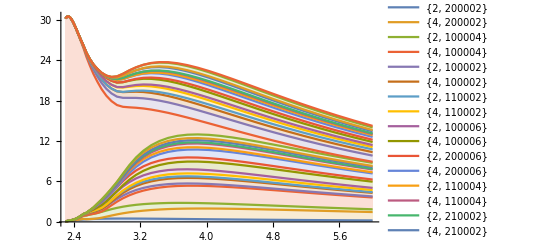

```mathematica
StackedListPlot[Second/@dat,PlotLegends->ToString/@First/@dat]
```

```mathematica
urqmdBRsNN=Block[{
totalSigma=Total@urqmdPartialSigmaNN},
Table[channel/totalSigma,{channel,urqmdPartialSigmaNN}]
];
```

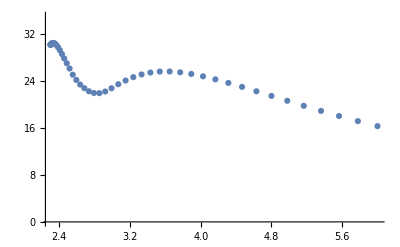

```mathematica
ListPlot[Transpose@{urqmdeCMNN,Total@urqmdPartialSigmaNN},PlotRange->{0,35}]
```

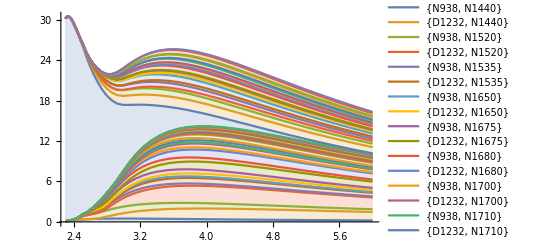

```mathematica
StackedListPlot[Evaluate@Table[Transpose@{urqmdeCMNN,channel},{channel,urqmdPartialSigmaNN}],PlotLegends->ToString/@urqmdProcessesNN]
```

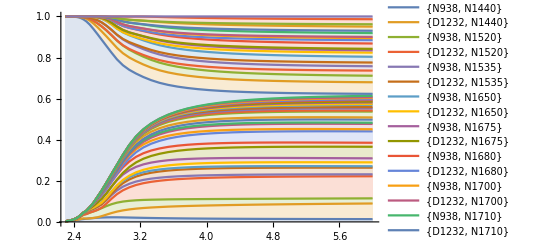

```mathematica
StackedListPlot[Evaluate@Table[Transpose@{urqmdeCMNN,channel},{channel,urqmdBRsNN}],PlotLegends->ToString/@urqmdProcessesNN]
```

```mathematica
urqmdInterpolNN=
Table[Interpolation[Transpose@{urqmdeCMNN,channel},InterpolationOrder->1],{channel,urqmdBRsNN}];
```

```mathematica
Table[f[4.],{f,urqmdInterpolNN}]
```

{0.0159461,0.0638108,0.0313966,0.103114,0.0123991,0.0329791,0.00872383,0.0177264,0.0231883,0.0481161,0.0234259,0.0486585,0.0127162,0.0230526,0.00680758,0.012929,0.012103,0.0225424,0.00535516,0.00617618,0.00633945,0.00581947,0.00417786,0.0044258,0.00397911,0.0029388,0.00368909,0.00229543,0.00366515,0.00229254,0.071723,0.0594759,0.0350985,0.0182671,0.0251309,0.0152858,0.0320301,0.0151381,0.012859,0.00537958,0.0268588,0.0103189,0.0105551,0.00407867,0.0206896,0.0079943,0.0201347,0.00653366,0.0242486,0.00741065}

```mathematica
dat = Transpose@{urqmdProcessesNN,Table[
Block[{data=Transpose@{urqmdeCMNN,channel}},
Table[Interpolation[data,m,InterpolationOrder->1],{m,2.3,6.0,0.1}]
],{channel,urqmdBRsNN}
]};
StringTemplate["`` --> ``"][pythiaName/@#[[1]],Length[#[[2]]]]&/@dat
```

{{N938, N1440} --> 38,{D1232, N1440} --> 38,{N938, N1520} --> 38,{D1232, N1520} --> 38,{N938, N1535} --> 38,{D1232, N1535} --> 38,{N938, N1650} --> 38,{D1232, N1650} --> 38,{N938, N1675} --> 38,{D1232, N1675} --> 38,{N938, N1680} --> 38,{D1232, N1680} --> 38,{N938, N1700} --> 38,{D1232, N1700} --> 38,{N938, N1710} --> 38,{D1232, N1710} --> 38,{N938, N1720} --> 38,{D1232, N1720} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, D1232} --> 38,{D1232, D1232} --> 38,{N938, D1600} --> 38,{D1232, D1600} --> 38,{N938, D1620} --> 38,{D1232, D1620} --> 38,{N938, D1700} --> 38,{D1232, D1700} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, D1905} --> 38,{D1232, D1905} --> 38,{N938, D1910} --> 38,{D1232, D1910} --> 38,{N938, D1920} --> 38,{D1232, D1920} --> 38,{N938, None} --> 38,{D1232, None} --> 38,{N938, D1950} --> 38,{D1232, D1950} --> 38}

```mathematica
dat = 
Function[ch,{idMask/@ch[[1]],ch[[2]]}]/@
Select[
Transpose@{urqmdProcessesNN,Table[Interpolation[Transpose@{urqmdeCMNN,channel},InterpolationOrder->1],{channel,urqmdPartialSigmaNN}]},
Function[ch,!FalseQ[pythiaName[ch[[1,1]]]≠None&&pythiaName[ch[[1,2]]]≠None]]
];
```

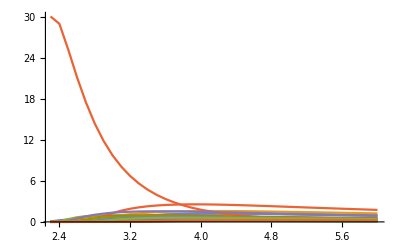

```mathematica
ListLinePlot[Table[Table[{m,f[m]},{m,2.3,6.,0.1}],{f,Second/@dat}],PlotRange->All]
```

```mathematica
Module[{stream},
stream=OpenWrite[atNotebook@"myFile"];
Table[WriteLine[stream,StringTemplate["  {``, Interpolator(2.3, 6.0, ``)},"][First@ch,Table[Second[ch]@m,{m,2.3,6.,0.1}]]],{ch,dat}];
Close[stream];
]
```

```mathematica
Second/@dat
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

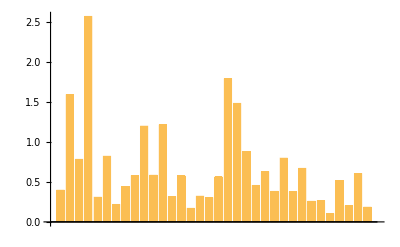

```mathematica
BarChart[Table[f[4.],{f,Second/@dat}]]
```

```mathematica
Block[{
total=Total@Table[f[4.],{f,Second/@dat}]
},
Table[f[4.]/total,{f,Second/@dat}]
]
```

{0.0176415,0.0705865,0.0347352,0.114066,0.0137178,0.0364826,0.00965145,0.0196088,0.0256535,0.0532239,0.0259164,0.0538242,0.0140682,0.0255,0.00753129,0.0143013,0.0133895,0.0249347,0.079383,0.0657964,0.0388291,0.0202053,0.0278026,0.0169083,0.0354347,0.0167442,0.0297127,0.0114127,0.0116768,0.00451109,0.0228883,0.00884201,0.0268246,0.00819561}